## Machine Learning Made Easy With Wolfram Mathematica in a Practical approach for I.R. 4.0 -Day 4

## Day#1--25/JAN/2021 2pm to 5pm Day#2--26/JAN/2021 2pm to 5pm Day#3--27/JAN/2021 2pm to 5pm Day#4--28/JAN/2021 2pm to 5pm

## Crash Course Day 4: Learning Objectives

#### Basic syntax in Wolfram Language IV

#### Unsupervised machine learning with Clustering

#### Accuracy measurements

#### Machine Learning with basic computer vision

#### Template Development II

#### Practical Applications

Predicting & Optimizing the performance of power plant

Quality prediction: Taste rating

Image Classification: Covid-19 Chest Imaging

## Syntax Review

## Import & Analytics

#### SetDirectory Import Correlation Counts Tally BinCounts Histogram BarChart

## Data Preparation

#### Thread RandomSample Complement IntegerPart DumpSave Get FindAnomalies threshold

## Machine Learning

#### Classify ClassifierMeasurements Predict PredictorMeasurements FindClusters

## Programming

#### Map /@ #$ Pure function Range Length ReplaceAll /.->

## Predicting & Optimizing the performance of power plant

temperature, in degrees Celsius.
exhaust_vacuum, in cm Hg.
ambient_pressure, in millibar.
relative_humidity, in percentage.
energy, in MW, net hourly electrical energy output.

Import a local Excel File contains contains 9568 samples with 4 independent variables collected from a combined cycle power plant over 6 years when the power plant was set to work with a full load. The measurements were taken every second.

```mathematica
SetDirectory[NotebookDirectory[]];
myImport=Import["combined_cycle_power_plant.xlsx",{"Data",1}] [[3;;]];
myHeader=Import["combined_cycle_power_plant.xlsx",{"Data",1}] [[1;;2]];
```

Check attribute of each record in each column

```mathematica
col=Length[myHeader[[1]]];
(*catogorize*)
Tally[Head/@myImport[[All,#]]]&/@Range[col]
Head/@myImport[[All,#]]&/@Range[col]
```

{{{Real,9568}},{{Real,9568}},{{Real,9568}},{{Real,9568}},{{Real,9568}}}

{1}
 |  |  |  |

Data Cleaning or Imputation

```mathematica
myImport=myImport/.""->Missing[];
```

Visualize the sample dependent variable -For numeric dependent variable (Use “Histogram”)

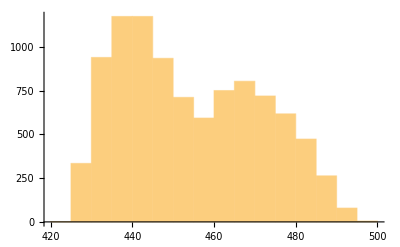

```mathematica
Histogram[myImport[[1;;,-1]]]
(*Count[myImport[[1;;,-1]]]*)
```

Use correlation matrix to determine the important input parameters

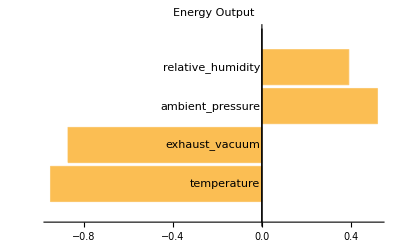

```mathematica
myCorrelations=Correlation[myImport][[-1,1;;-2]];
BarChart[myCorrelations, BarOrigin->Left,ChartLabels->myHeader[[2]],PlotLabel->"Energy Output"]
```

Quick Data Transformation

```mathematica
myData=Thread[myImport[[1;;,1;;-2]]->myImport[[1;;,-1]]];
```

Detect potential clusters, to see if different machine learning algorithms should be applied.

```mathematica
myClusters=FindClusters[myData,4];
(*how big is the array*)
Length[myClusters]
```

4

Constructing Profile by Clusters -For numeric dependent variable (Use “Histogram”)

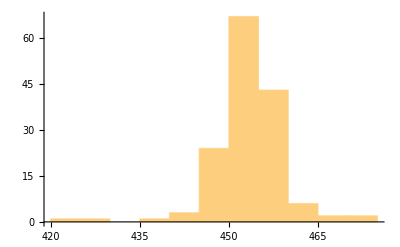

```mathematica
(*if something are incontinuos, pick type of cluster*)
histplot=Histogram[myClusters[[3]]]
```

Visualized the fitted cluster as a PDF (probability density function using SmoothKernel Distribution)

```mathematica
cluster=1;

histplot=Histogram[myClusters[[cluster]],Automatic,"PDF"];
dist=SmoothKernelDistribution[myClusters[[cluster]]];

Show[histplot,
Plot[PDF[dist,x],{x,408,508}]]
```

Visualized all fitted clusters as a PDF (probability density function)

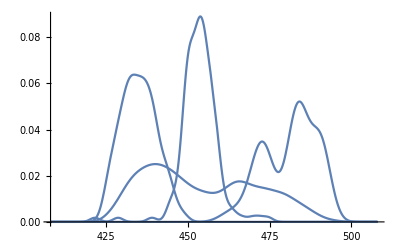

```mathematica
dist=SmoothKernelDistribution[myClusters[[#]]]&/@Range[Length[myClusters]];
(*smothhing the bar*)
Plot[PDF[
dist[[#]],x]&/@Range[Length[myClusters]
],{x,408,508},PlotRange->All]
```

Train a Predictor using 80% of the extracted data, use the remaining 20% for the accuracy testing later:

```mathematica
sampleSize=IntegerPart[Length@myData*0.8];
myDataTrain=RandomSample[myData,sampleSize];
myDataTest=Complement[myData,myDataTrain];
```

Auto-train the model using predict

```mathematica
myPredict=Predict[myDataTrain]
```

PredictorFunction[…]

Accuracy Check for Predictor

```mathematica
myAccuracy=PredictorMeasurements[myPredict,myDataTest];
myAccuracy["Report"]
```

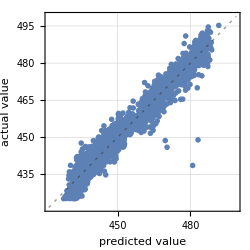
```mathematica
{{"Predictor Measurements"}, {{{Predictor method, GradientBoostedTrees}, {Number of test examples, 1898}, {Standard deviation, 3.8290018329105826034`3." ± "0.1645015558092939312`2.}, {Standard deviation baseline, 17.0197765880742757361`3." ± "0.1929266183166493676`2.}, {R-squared, 0.9493868416916115827`3." ± "0.0044977509504017243`2.}, {Mean cross entropy, 2.7858664710411242815`3." ± "0.0577374888394985852`2.}, {Single evaluation time, Quantity[7.41, ("Milliseconds")/("Examples")]}, {Batch evaluation speed, Quantity[1.33, ("Examples")/("Milliseconds")]}, {-Graphics-, }}}}
(*clustering also allow to remove the white noise*)
```

Accuracy Check-Mean Cross Entropy

Mean Cross-Entropy = 0.00: Perfect prediction.
Mean Cross-Entropy < 0.02: Great prediction.
Mean Cross-Entropy < 0.05: Good prediction.
Mean Cross-Entropy < 0.20: Acceptable.
Mean Cross-Entropy > 0.30: Not very good.
Mean Cross-Entropy > 1.00: Terrible.
Mean Cross-Entropy > 2.00 Something is very wrong!

Understanding standard deviation & standard deviation baseline

```mathematica
myAccuracy[{"MeanSquare"}]
(*sometime mean cross tooighh entropy can be use on this*)
```

{14.6613}

Accuracy Check-R Squared

The coefficient of determination, denoted R2 or r2 and pronounced “R squared”, is the proportion of the variance in the dependent variable that is predictable from the independent variable(s). Thus for a perfect fit, the correlation coefficient R2 would be 1. As we have R2 = 0.95, the model is predicting very well the testing data.

```mathematica
myAccuracy[{"MeanSquare","RSquared"}]
```

{14.6613,0.949387}

Accuracy Check-Summary Overview

Accuracy: 3.71 Standard Deviation comparing to baseline Standard Deviation 16.8
Mean Cross Entropy: 2.74 -Something Wrong
R squared (R2): 0.95 -very good

Saving the trained Predictor for future use

```mathematica
DumpSave["Energy.mx",myPredict]
```

{PredictorFunction[…]}

We may retrieve the trained machine learning model anytime for immediate use.

```mathematica
Get["Energy.mx",myPredict];
(*change method*)
(*Classify[dataset,Method->"LogisticRegression"]*)
```

## Quality prediction: Taste rating

Import a local Excel File

```mathematica
SetDirectory[NotebookDirectory[]];
myImport=Import["DrinkQuality.xlsx",{"Data",1}] [[3;;]];
myHeader=Import["DrinkQuality.xlsx",{"Data",1}] [[1;;2]];
```

Check attribute of each record in each column

```mathematica
col=Length[myImport[[1]]];
Tally[Head/@myImport[[All,#]]]&/@Range[col]
```

{{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}},{{Real,3600}}}

Data Cleaning or Imputation

```mathematica
myImport=myImport/.""->Missing[];
```

Visualize the sample dependent variable

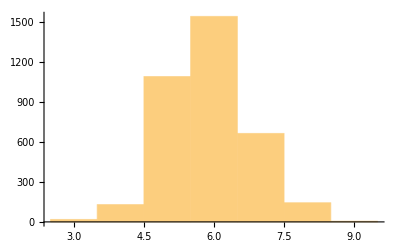

```mathematica
Histogram[myImport[[1;;,-1]]]
```

Find anomalous data on a numeric dataset

```mathematica
myAnomalies=FindAnomalies[myImport];
```

Use correlation matrix to determine the important input parameters

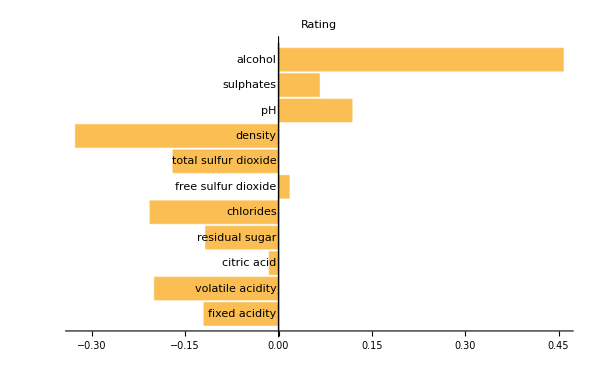

```mathematica
myCorrelations=Correlation[myImport][[-1,1;;-2]];
BarChart[myCorrelations, BarOrigin->Left,ChartLabels->myHeader[[2]],PlotLabel->"Rating"]
```

Quick Data Transformation

```mathematica
myData=Thread[myImport[[All,1;;-2]]->myImport[[All,-1]]];
```

Detect potential clusters, to see if different machine learning algorithms should be applied.

```mathematica
myClusters=FindClusters[myData,4];
Length[myClusters]
```

4

Visualized the fitted cluster as a PDF (probability density function using SmoothKernel Distribution)

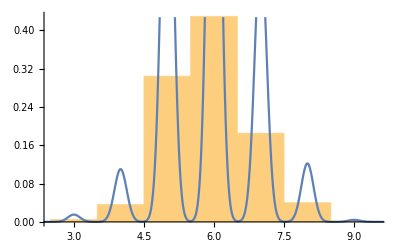

```mathematica
cluster=1;

histplot=Histogram[myClusters[[cluster]],Automatic,"PDF"];
dist=SmoothKernelDistribution[myClusters[[cluster]]];

Show[histplot,
Plot[PDF[dist,x],{x,2,10}]]
```

Visualized all fitted clusters as a PDF (probability density function)

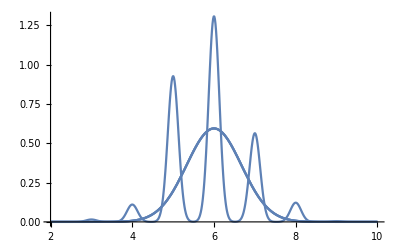

```mathematica
dist=SmoothKernelDistribution[myClusters[[#]]]&/@Range[Length[myClusters]];

Plot[PDF[
dist[[#]],x]&/@Range[Length[myClusters]
],{x,2,10},PlotRange->All]
```

Train a predictor using 80% of the extracted data, use the remaining 20% for the accuracy testing.

```mathematica
sampleSize=IntegerPart[Length@myData*0.8];
myDataTrain=RandomSample[myData,sampleSize];
myDataTest=Complement[myData,myDataTrain];
```

Auto-train the model using predict

```mathematica
(*convert into classify for testibf later*)
myPredict=Predict[myDataTrain]
```

PredictorFunction[…]

Accuracy Check for Predictor

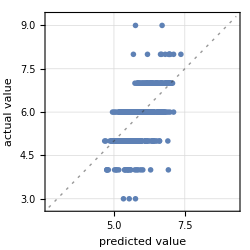
Predictor Measurements
Predictor method | RandomForest
Number of test examples | 483
Standard deviation | 0.733 ± 0.033
Standard deviation baseline | 0.901 ± 0.033
R-squared | 0.339 ± 0.076
Mean cross entropy | 1.11 ± 0.049
Single evaluation time | 6.08 ms/example
Batch evaluation speed | 1.38 examples/ms
-Graphics- |

```mathematica
myAccuracy=PredictorMeasurements[myPredict,myDataTest];
myAccuracy["Report"]
```

Accuracy Check-Mean Cross Entropy

Mean Cross-Entropy = 0.00: Perfect prediction.
Mean Cross-Entropy < 0.02: Great prediction.
Mean Cross-Entropy < 0.05: Good prediction.
Mean Cross-Entropy < 0.20: Acceptable.
Mean Cross-Entropy > 0.30: Not very good.
Mean Cross-Entropy > 1.00: Terrible.
Mean Cross-Entropy > 2.00 Something is very wrong!

Understanding standard deviation & standard deviation baseline

```mathematica
myAccuracy[{"MeanSquare"}]
```

Accuracy Check-R Squared

The coefficient of determination, denoted R2 or r2 and pronounced “R squared”, is the proportion of the variance in the dependent variable that is predictable from the independent variable(s). Thus for a perfect fit, the correlation coefficient R2 would be 1.

```mathematica
myAccuracy[{"RSquared"}]
```

Accuracy Check-Summary Overview

Accuracy: 0.73 Standard Deviation comparing to baseline Standard Deviation 0.93
Mean Cross Entropy: 1.10 Terrible?
R squared (R2): 0.384 needs more investigation

Saving the trained Predictor for future use

```mathematica
DumpSave["Drink.mx",myPredict];
```

We may retrieve the trained machine learning model anytime for immediate use.

```mathematica
Get["Drink.mx",myPredict];
```

Test Output

Actual sample {8.6,0.23,0.4,4.2,0.035,17,109,0.9947,3.14,0.53,9.7} -> 5
Actual sample {6.2,0.66,0.48,1.2,0.029,29,75,0.9892,3.33,0.39,12.8}->8
Actual sample {6.8,0.26,0.42,1.7,0.049,41,122,0.993,3.47,0.48,10.5}->8

```mathematica
Specimen = {6.8,0.26,0.42,1.7,0.049,41,122,0.993,3.47,0.48,10.5};
myPredict[Specimen, "Distribution"]
(*+2.24*)
```

NormalDistribution[6.62531,0.700134]

Simple Batch Import

```mathematica
(*scheduler task*)
BatchSpecimens=Import["DrinkQuality_Production.xlsx",{"Data",1}] [[3;;]];
myResult=myPredict[BatchSpecimens]
```

{5.64955,5.81525,5.94412,5.88889,5.79684,6.91988,5.59432,5.64955,5.98094}

Simple Batch Output

```mathematica
exportResult=Append[BatchSpecimens[[#]],myResult[[#]]]&/@Range[Length[BatchSpecimens]];
Export["Output.xlsx",exportResult];
```

## Extracting the Clustered Data

Using a Day-3 example as an illustration

```mathematica
myData={{-1.1,2.6},{3.9,-0.8},{4.2,-3.7},{3.3,3.5},{3.9,5.2},{4.1,-4.8},{3.8,3.7},{5.6,0.1},{3.1,-5.2},{-0.9,2.3},{2.9,4.1},{-2.3,3.9},{-2.5,3.},{2.6,-5.5},{5.2,1.9},{-0.7,1.3},{0.9,2.8},{-1.5,3.3},{3.8,1.2},{2.6,-5.1},{-0.8,3.2},{4.7,0.7},{3.,3.},{3.9,3.6},{4.5,1.4},{4.2,1.3},{-1.1,2.6},{4.8,2.4},{3.3,-3.5},{3.2,-4.6},{3.3,-4.9},{3.,3.5},{0.7,2.1},{3.2,-4.3},{-2.,0.5},{-1.2,2.},{-1.6,1.8},{-3.5,3.7},{4.8,0.2},{3.3,2.4},{-0.1,2.1},{-1.3,2.5},{4.4,3.9},{3.5,0.2},{0.1,2.9},{-1.,1.6},{-1.4,4.5},{3.2,2.5},{-1.6,2.4},{2.6,-5.1}};
```

```mathematica
myDataLabel={{-1.1,2.6}->"A",{3.9,-0.8}->"A",{4.2,-3.7}->"A",{3.3,3.5}->"B",{3.9,5.2}->"A",{4.1,-4.8}->"C",{3.8,3.7}->"A",{5.6,0.1}->"D",{3.1,-5.2}->"A",{-0.9,2.3}->"B",{2.9,4.1}->"A",{-2.3,3.9}->"B",{-2.5,3.}->"C",{2.6,-5.5}->"C",{5.2,1.9}->"C",{-0.7,1.3}->"B",{0.9,2.8}->"C",{-1.5,3.3}->"A",{3.8,1.2}->"A",{2.6,-5.1}->"B",{-0.8,3.2}->"A",{4.7,0.7}->"A",{3.,3.}->"A",{3.9,3.6}->"B",{4.5,1.4}->"C",{4.2,1.3}->"B",{-1.1,2.6}->"C",{4.8,2.4}->"A",{3.3,-3.5}->"A",{3.2,-4.6}->"A",{3.3,-4.9}->"B",{3.,3.5}->"C",{0.7,2.1}->"A",{3.2,-4.3}->"A",{-2.,0.5}->"A",{-1.2,2.}->"B",{-1.6,1.8}->"A",{-3.5,3.7}->"C",{4.8,0.2}->"B",{3.3,2.4}->"C",{-0.1,2.1}->"A",{-1.3,2.5}->"A",{4.4,3.9}->"A",{3.5,0.2}->"A",{0.1,2.9}->"B",{-1.,1.6}->"A",{-1.4,4.5}->"A",{3.2,2.5}->"A",{-1.6,2.4}->"A",{2.6,-5.1}->"C"};
```

```mathematica
myClusters=FindClusters[myData];
{ListPlot[myDataLabel],ListPlot[myClusters]}
```

Perform clustering and extract the record ID

Import data and transform

```mathematica
SetDirectory[NotebookDirectory[]];
myImport=Import["Clusters.xlsx",{"Data",1}] [[3;;]];
myHeader=Import["Clusters.xlsx",{"Data",1}] [[1;;2]];
myData=myImport[[All,1;;-2]];
myDataLabel=Thread[myImport[[All,1;;-2]]->myImport[[1;;,-1]]];
```

Visualize clusters. This only works for 2-dimensional numeric matrix. So we may skip this part.

```mathematica
myClusters=FindClusters[myData]
{ListPlot[myDataLabel],ListPlot[myClusters]}
```

Perform clustering and extract the ID

```mathematica
myClusterID=FindClusters[myDataLabel]
```

Export the cluster entities by ID

```mathematica
Export["myClusterID.xlsx",myClusterID]
```

## Image Classification: Covid-19 Chest Imaging

https://www.kaggle.com/khoongweihao/covid19-xray-dataset-train-test-sets
In late January, a Chinese team published a paper detailing the clinical and paraclinical features of COVID-19. They reported that patients present abnormalities in chest CT images with most having bilateral involvement Huang 2020. Bilateral multiple lobular and subsegmental areas of consolidation constitute the typical findings in chest CT images of intensive care unit (ICU) patients on admission Huang 2020. In comparison, non-ICU patients show bilateral ground-glass opacity and subsegmental areas of consolidation in their chest CT images Huang 2020. In these patients, later chest CT images display bilateral ground-glass opacity with resolved consolidation Huang 2020.

Define the image directories

```mathematica
SetDirectory[NotebookDirectory[]];
neg=FileNames[All,"xray_dataset_covid19\\NORMAL"];
pos=FileNames[All,"xray_dataset_covid19\\PNEUMONIA"];
```

Mass-labelling the images

```mathematica
(*neg[[50]]-> "Negative"*)
(*mass all label in the folder *)
DataNeg=neg[[#]]->"Negative"&/@Range[Length@neg];
DataPos=pos[[#]]->"Positive"&/@Range[Length@pos];
```

Basic data transformations

```mathematica
(*combine all the data*)
Data=Union[DataNeg,DataPos];
Length@Data
```

188

Import all image files to the required machine-learning format

```mathematica
(*data type *)
Data[[1]][[2]]
```

```mathematica
myData=Import@Data[[#]][[1]]->Data[[#]][[2]]&/@Range[Length@Data];
```

Train a classifier using 80% of the extracted data, use the remaining 20% for the accuracy testing later:

```mathematica
sampleSize=IntegerPart[Length@myData*0.8];
myDataTrain=RandomSample[myData,sampleSize];
myDataTest=Complement[myData,myDataTrain];
```

Auto-train the model

```mathematica
myClassify=Classify[myDataTrain(*,TargetDevice->"GPU"*)]
```

ClassifierFunction[…]

Accuracy Check

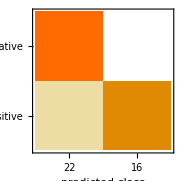
Classifier Measurements
Classifier method | LogisticRegression
Number of test examples | 38
Accuracy | (97.42.6) %
Accuracy baseline | (55.8.) %
Geometric mean of probabilities | 0.908 ± 0.064
Mean cross entropy | 0.097 ± 0.07
Single evaluation time | 70. ms/example
Batch evaluation speed | 17.3 examples/s
-Graphics- |

```mathematica
myAccuracyDiag=ClassifierMeasurements[myClassify,myDataTest];
myAccuracyDiag["Report"]
```

Accuracy Check-Mean Cross Entropy

Mean Cross-Entropy = 0.00: Perfect prediction.
Mean Cross-Entropy < 0.02: Great prediction.
Mean Cross-Entropy < 0.05: Good prediction.
Mean Cross-Entropy < 0.20: Acceptable.
Mean Cross-Entropy > 0.30: Not very good.
Mean Cross-Entropy > 1.00: Terrible.
Mean Cross-Entropy > 2.00 Something is very wrong!

Accuracy Check-ROC Curve

A good measure for the precision of a binary classification model is the ROC curve (receiver operating characteristic curve). We are interested in the area under the curve (AUC). A perfect classifier would have an AUC=1, and a random one would have AUC=0.5. Our model has an AUC = 0.83, which is great.

```mathematica
myAccuracyDiag["AreaUnderROCCurve"]
```

Accuracy Check-Summary Overview

Accuracy:  ____comparing to baseline accuracy ____ 
Type I error:   __/__   =____% (wrongly identifying healthy test subjects as Covid-19)
Type II error: __/__   =____% (wrongly identifying  Covid-19 test subjects as healthy)

Mean Cross Entropy: 
Area under ROC: